## Research Tasks Geometry

## Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<Geometry`
```

## Test-Preamble

```mathematica
(* AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace\\Geometry"];
<<Geometry` *)
```

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
<<TestAlgebra` 
<<Geometry`
```

Get::noopen: Cannot open TestAlgebra`.

$Failed

Get::noopen: Cannot open Geometry`.

$Failed

```mathematica
nCollatz[16]
```

{16,8,4,2,1}

## Archived Notes

## Apps

### Case 0

```mathematica
Options[gPolygon]
```

{FaceColor→RGBColor[1, 0, 0],FaceOpacity→1,EdgeColor→GrayLevel[0],EdgeOpacity→1,Thickness→0.0125,Dashing→{2 π,2 π}}

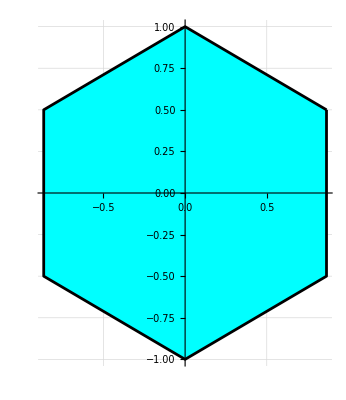

```mathematica
gPolygon[pGon[6],Thickness->0.005,FaceColor->Cyan]//toGL//gr1
```

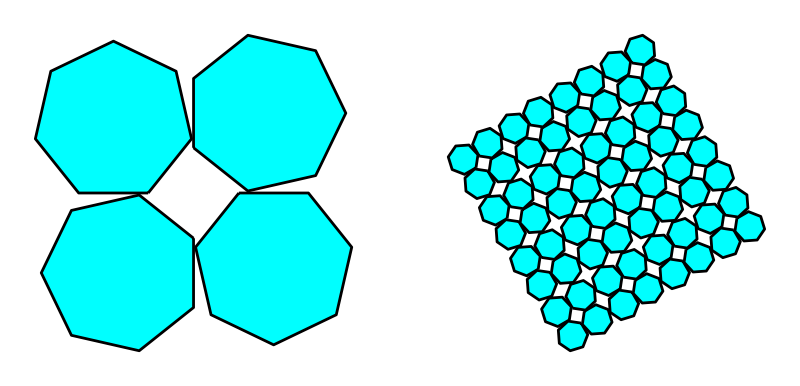

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}]}]

dpoly:={{{1,{{0,0},{1,0},{1,1},{.5,4.0},{0,1}}},{White,1}},{Black,1,.005,2 π,2 π}}
dpoly:={tra3[newGeo[3,RGBColor[.55,.55,.25,.5]][[1]],{1,1}],{Black,1,.005,2 π,2 π}}

dpoly:=tra3[gPolygon[pGon[7],Thickness->0.005,FaceColor->Cyan],{1,1}]

GraphicsRow[
{
Graphics[Nest[teil,dpoly,1]//toGL],
Graphics[rot3[Nest[teil,dpoly,3],{30 Degree,{0,0}}]//toGL//gr]
}
]
```

### Case 1

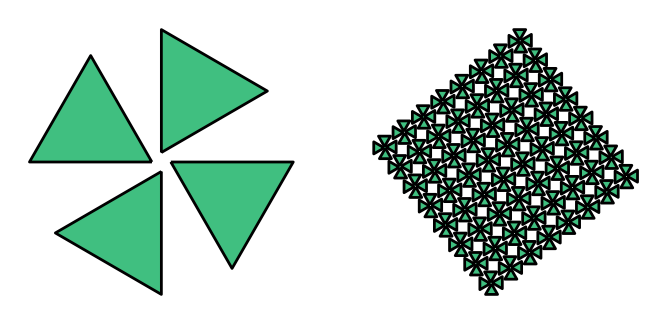

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}]}]

dpoly:=tra3[newGeo[6],{2,1}]
dpoly:={{{1,{{0,0},{1,0},{1,1},{.5,4.0},{0,1}}},{White,1}},{Black,1,.005,2 π,2 π}}

dpoly:={tra3[newGeo[3,RGBColor[.25,.75,.5,.5]][[1]],{1,1}],{Black,1,.005,2 π,2 π}}
GraphicsRow[{Graphics[Nest[teil,dpoly,1]//toGL],
Graphics[rot3[Nest[teil,dpoly,4],{30 Degree,{0,0}}]//toGL]}]
```

```mathematica
nGonAtEdge3[fig_,{m_,n_}]:=trf3[
trf3[
newGeo[n],
toUnit[toEdges[newGeo[n]][[1,1,1,2]]]//N
],
toVector[toEdges[fig][[m,1,1,2]]]
]
```

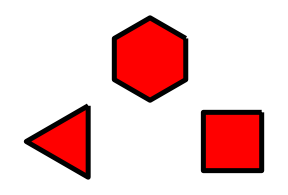

```mathematica
dpoly1:=tra3[newGeo[3],{0,0}]
dpoly2:=tra3[newGeo[4],{4,0}]
dpoly3:=tra3[newGeo[6],{2,2}]
Graphics[{dpoly1,dpoly2,dpoly3}]//toGL
```

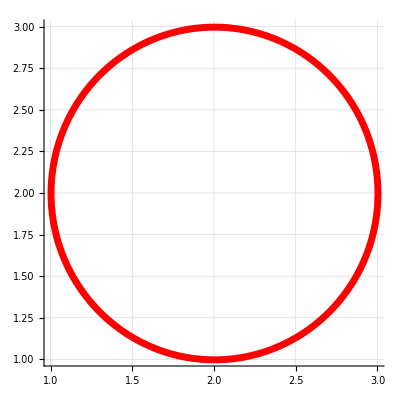

```mathematica
cCircle[{2,2},1]//toGL//gr1
```

### Case 2

```mathematica
cCircle[{5,5},1.5]//toGL
```

{RGBColor[0, 1, 1],Opacity[1],{Thickness[0.0025],Dashing[{2 π,2 π}],Circle[{5,5},1.5]}}

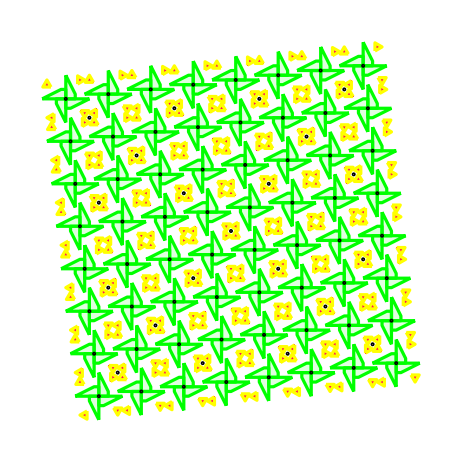

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}],
repCol[cCircle[rotp,.25],{Black}]
}]

dpolyA:={tra3[newGeo[3,RGBColor[1,.05,.35,.1]][[1]],{1,1}],{Yellow,1,.005,2 π,2 π}}
dpolyB:={{{1,{{4,0},{4,5},{2,5},{2,4}}},{LightGreen,1}},{Green,1,.005,2 π,2 π}}
Nest[teil,{dpolyB,dpolyA},4]//toGL//gr
```

### Case 3

```mathematica
ind:=Tuples[Composition@@{sym4ref,sym4rot},3]
```

```mathematica
dpoly:={{{1,{{0,0},{0.5,0.2},{1,1},{0.2,0.9}}},{RGBColor[1, 0.9500000000000001, 0],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpoly:={{{1,{{0,0},{1,0},{0.7,1},{0.3,1}}},{RGBColor[0.87, 0.87, 0.87, 0.9],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpoly:={{{1,{{0,0},{0.25,0},{0.5,0.25},{0.5,.5}}},{RGBColor[0.87, 0.87, 0.87, 0.9],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
sym4rot[sym4ref[dpoly]]//toGL//gr1
```

-Graphics-

```mathematica
Table[ind[[k]][dpoly]//toGL//gr,{k,1,Length[ind]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Case 4 ( IN-DEVELOPMENT )

```mathematica
dpoly0:={{{1,{{0.25,0.0},{0.5,0.0},{0.5,0.75},{0.75,0.75},{0.75,1.0},{0.0,1.0},{0.0,0.75},{0.25,0.75}}},{Cyan,1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpolyA:={{{1,{{0.5,0},{1,0.5},{1,1},{0.5,0.5},{0,1},{0,.5}}},{RGBColor[0.87, 0.87, 0.87, 0.9],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpolyB:={{{1,{{0,0},{0.5,0},{0,0.5}}},{Cyan,1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpolyC:={{{1,{{0.5,0},{1,0},{1,0.5}}},{Cyan,1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpoly:={dpolyA,dpolyB,dpolyC}
dpoly//toGL//gr1;
sym4ovr1[dpoly]//toGL//gr1
```

-Graphics-

```mathematica
sym4ovr1[figke_]:=Module[{rotp},
rotp={1,1};
tra3[Scale[
{
figke,
rot3[ref3[figke,{{1,0},rotp}],{π,{1.5,0.5}}],
tra3[figke,{1,1}],
tra3[rot3[ref3[figke,{{1,0},rotp}],{π,{1.5,0.5}}],{-1,1}]
},
.5],{-.5,-.5}]]
```

```mathematica
ind:=Tuples[Composition@@{sym4rot,sym4ref,sym4ovr1},3]
Table[ind[[k]][dpoly]//toGL//gr,{k,1,Length[ind]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ind//TableForm
```

sym4rot@*sym4rot@*sym4rot
sym4rot@*sym4rot@*sym4ref
sym4rot@*sym4rot@*sym4ovr1
sym4rot@*sym4ref@*sym4rot
sym4rot@*sym4ref@*sym4ref
sym4rot@*sym4ref@*sym4ovr1
sym4rot@*sym4ovr1@*sym4rot
sym4rot@*sym4ovr1@*sym4ref
sym4rot@*sym4ovr1@*sym4ovr1
sym4ref@*sym4rot@*sym4rot
sym4ref@*sym4rot@*sym4ref
sym4ref@*sym4rot@*sym4ovr1
sym4ref@*sym4ref@*sym4rot
sym4ref@*sym4ref@*sym4ref
sym4ref@*sym4ref@*sym4ovr1
sym4ref@*sym4ovr1@*sym4rot
sym4ref@*sym4ovr1@*sym4ref
sym4ref@*sym4ovr1@*sym4ovr1
sym4ovr1@*sym4rot@*sym4rot
sym4ovr1@*sym4rot@*sym4ref
sym4ovr1@*sym4rot@*sym4ovr1
sym4ovr1@*sym4ref@*sym4rot
sym4ovr1@*sym4ref@*sym4ref
sym4ovr1@*sym4ref@*sym4ovr1
sym4ovr1@*sym4ovr1@*sym4rot
sym4ovr1@*sym4ovr1@*sym4ref
sym4ovr1@*sym4ovr1@*sym4ovr1

## Test Möbius Transformations

```mathematica
FileNameJoin[{$InstallationDirectory,"SystemFiles","Components","AutoCompletionData","Main","OptionValues"}]
```

C:\Program Files\Wolfram Research\Mathematica\12.3.1\SystemFiles\Components\AutoCompletionData\Main\OptionValues

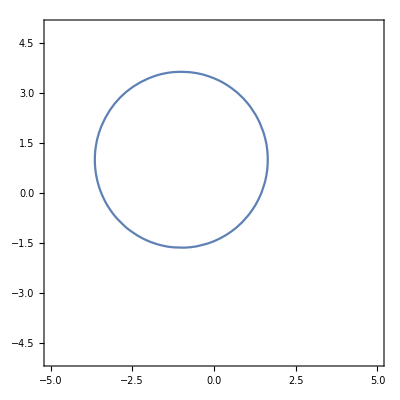

```mathematica
ClearAll[x,y]
ContourPlot[x^2+y^2+2x-2y-5==0,{x,-5,5},{y,-5,5},Axes->True]
```

```mathematica
(3z Conjugate[z]//ComplexExpand)/.z:>x+I y//Expand
```

```mathematica
z Conjugate[z]/. z-> x+I y
```

(x+ⅈ y) (Conjugate[x]-ⅈ Conjugate[y])

```mathematica
3(x+I y)(x-I y)//Expand
```

3 x^2+3 y^2

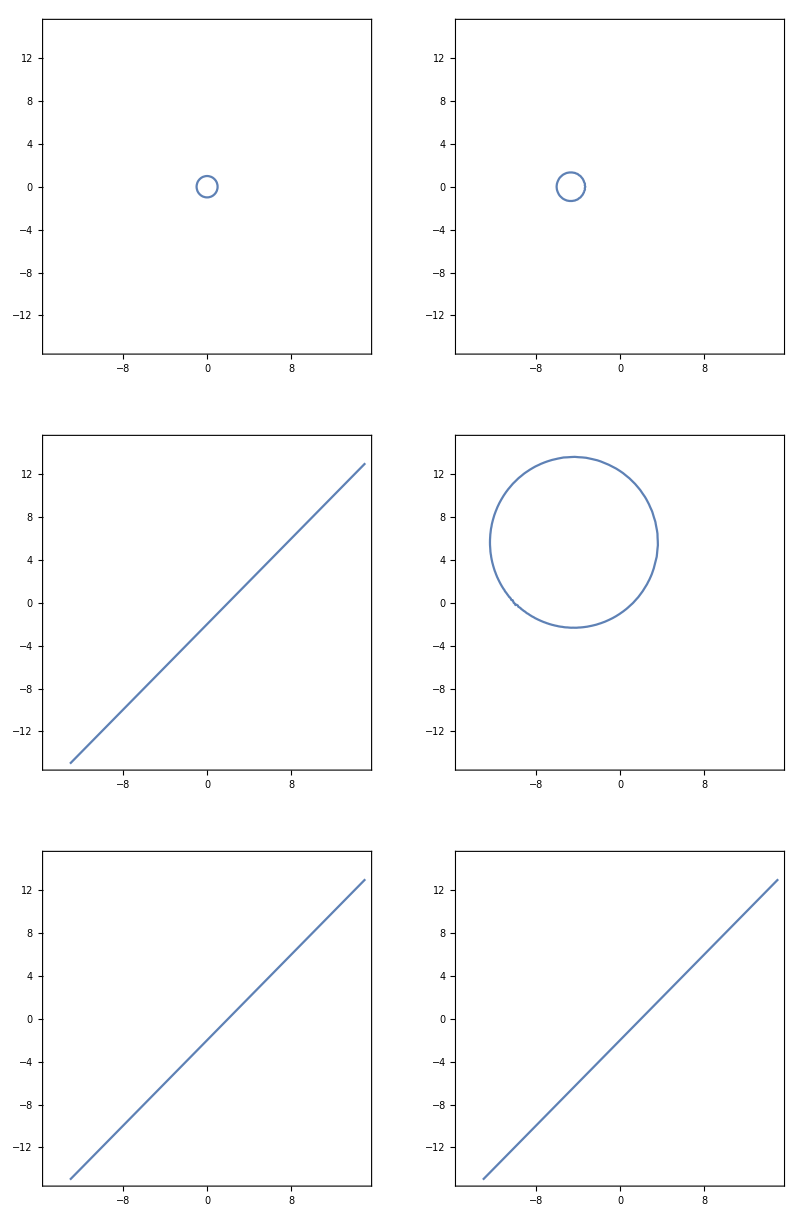

```mathematica
eqn1=ComplexExpand[z Conjugate[z]-1/.z->(1z+0)/(0z+1),z]/.{Re[z]->x,Im[z]->y};
eqn2=ComplexExpand[z Conjugate[z]-1/.z->(0.5z+1)/(1z+4),z]/.{Re[z]->x,Im[z]->y}//FullSimplify;
eqn3=ComplexExpand[Im[z]-Re[z]+2/.z->(1z+0)/(0z+1),z]/.{Re[z]->x,Im[z]->y};
eqn4=ComplexExpand[Im[z]-Re[z]+2/.z->(z+1)/(.1z+1),z]/.{Re[z]->x,Im[z]->y};
eqn5=ComplexExpand[Im[z]-Re[z]+2/.z->(z+0)/(0z+1),z]/.{Re[z]->x,Im[z]->y};
eqn6=ComplexExpand[Im[z]-Re[z]+2/.z->(z+2)/(.1z+1)/.z->(1z-2)/(-.1z+1),z]/.{Re[z]->x,Im[z]->y};

a=15;
GraphicsGrid[{
{
ContourPlot[eqn1==0,{x,-a,a},{y,-a,a},Axes->True],
ContourPlot[eqn2==0,{x,-a,a},{y,-a,a},Axes->True]},
{ContourPlot[eqn3==0,{x,-a,a},{y,-a,a},Axes->True],
ContourPlot[eqn4==0,{x,-a,a},{y,-a,a},Axes->True]},
{ContourPlot[eqn5==0,{x,-a,a},{y,-a,a},Axes->True],
ContourPlot[eqn6==0,{x,-a,a},{y,-a,a},Axes->True]
}
}]
```

```mathematica
z Conjugate[z]-1/.z->(1z-5)/(0z+5)//Expand
```

-z/5-Conjugate[z]/5+1/25 z Conjugate[z]

```mathematica
m:={{4,9},{11,25}};
t:={{1,1},{0,1}};
```

```mathematica
m//mf
m.Inverse[t]//mf
m.Inverse[t].Inverse[t]//mf
m.MatrixPower[Inverse[t],5]//mf
```

(4 | 9
11 | 25)

(4 | 5
11 | 14)

(4 | 1
11 | 3)

(4 | -11
11 | -30)

```mathematica
Clear[a,b,c,d]
ma={{a,b},{c,d}};
mt={{1,1},{0,1}};
ms={{0,-1},{1,0}};
mst={{0,-1},{1,1}};
```

```mathematica
mst.ma.Inverse[mst]//mf
```

(-c+d | -c
a-b+c-d | a+c)

```mathematica
mt.{1,0}.Inverse[mt]
```

{1,-1}

```mathematica
maa={{5,2},{-2,3}};
maa={{b+d,b},{-b,d}};
maa1={{a,-c},{c,a+c}};
{mst.maa,maa.mst}
{mst.maa1,maa1.mst}
```

{{{b,-d},{d,b+d}},{{b,-d},{d,b+d}}}

{{{-c,-a-c},{a+c,a}},{{-c,-a-c},{a+c,a}}}

```mathematica
mm={{1,0,1,-1},{0,1,1,0},{1,-1,0,-1},{1,0,1,-1}};
```

```mathematica
MatrixRank[mm]
NullSpace[mm]
RowReduce[mm]
```

2

{{1,0,0,1},{-1,-1,1,0}}

{{1,0,1,-1},{0,1,1,0},{0,0,0,0},{0,0,0,0}}

```mathematica
mm.{-1,-1,1,0}
```

{0,0,0,0}

```mathematica
maa2=a mst+b IdentityMatrix[2];
maa2=a IdentityMatrix[2] + b mst+c Inverse[mst]
mst.maa2//mf
maa2.mst//mf
```

{{a+c,-b+c},{b-c,a+b}}

(-b+c | -a-b
a+b | a+c)

(-b+c | -a-b
a+b | a+c)

```mathematica
mst//mf
Inverse[mst]//mf
```

(0 | -1
1 | 1)

(1 | 1
-1 | 0)

```mathematica
Graphics3D[{Opacity[0.6],Octahedron[],Circumsphere[Octahedron[]]}]
```

-Graphics3D-

## Lines-UZT-1

```mathematica
p1:={0,0};
p2:={3,1};
p3:={1,3};
p4:={4,3};
p5:={-2,3};
Graphics[{
Arrow[{p1,p5}],
Line[{p1,p2}],
HalfLine[{p1,p4}],
Dashed,InfiniteLine[{p1,p3}]
},
AxesOrigin->{0,0},Axes->True,AxesLabel->{"X","Y"},
PlotRange->{{-5,5},{-5,5}}]
```

-Graphics-

```mathematica
tra3cp[figs_,t_]:={figs,figs/.f:pnt:>TranslationTransform[t][f]}
```

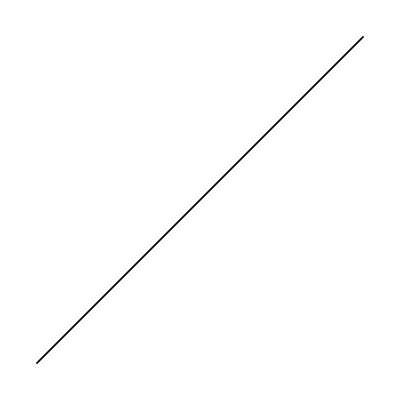

```mathematica
tra3cp[{Line[{{0,0},{1,1}}]},{0,0}]//toGL//Graphics
```

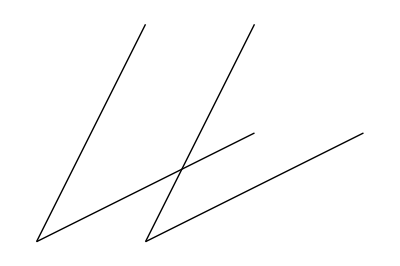

```mathematica
tra3cp[{Line[{{0,0},{4,2}}],Line[{{0,0},{2,4}}]},{-2,0}]//toGL//Graphics
```

```mathematica
trans[figke_]:= Module[{},
{
figke,
tra3cp[figke,{1,0}]
}
]
line:={Line[{{0,0},{4,2}}]}
```

```mathematica
Fold[tra3cp,line,Table[{1,1},{k,1}]]//tf
```

Line[{{0,0},{4,2}}]
Line[{{1,1},{5,3}}]

```mathematica
Fold[tra3cp,line,Table[{k,k},{k,2}]]//tf
```

Line[{{0,0},{4,2}}] | Line[{{1,1},{5,3}}]
Line[{{2,2},{6,4}}] | Line[{{3,3},{7,5}}]

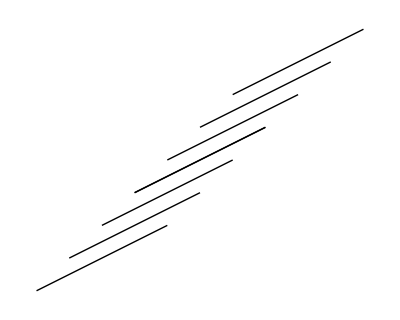

```mathematica
Fold[tra3cp,line,Table[{k,k},{k,3}]]//toGL//Graphics
```

## Lines-UZT-2

```mathematica
Table[ReIm[ⅇ^((k 2 Pi I)/4)],{k,0,3}]//tf
Table[ReIm[ⅇ^((k 2 Pi I)/8)],{k,0,7}]//tf
```

1 | 0
0 | 1
-1 | 0
0 | -1

1 | 0
1/(√2) | 1/(√2)
0 | 1
-1/(√2) | 1/(√2)
-1 | 0
-1/(√2) | -1/(√2)
0 | -1
1/(√2) | -1/(√2)

```mathematica
lines[n_]:=Map[Line[{{0,0},#}]&,Table[ReIm[ⅇ^((k 2 Pi I)/n)],{k,0,n-1}]]
{{{1,{{0,0},#}},{White,1}},{Black,1,.005,2 π,2 π}};
lines[n_]:=Map[{{{1,{{0,0},#}},{Red,1}},{Blue,1,.005,2 π,2 π}}&,Table[ReIm[ⅇ^((k 2 Pi I)/n)],{k,0,n-1}]]
```

```mathematica
GraphicsRow[{
lines[18]//toGL//Graphics
}]
```

-Graphics-

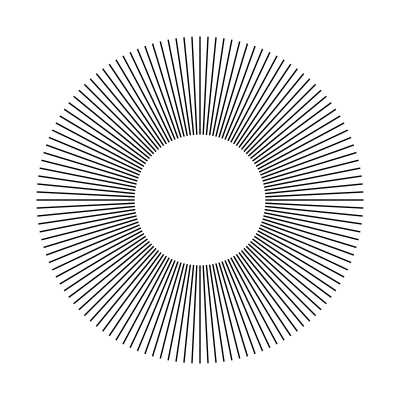

```mathematica
lines2[n_]:=Map[Line[{0.4#[[2]],#[[2]]}]&,Table[{(k+1)/n ReIm[ⅇ^((k 2 Pi I)/n)],ReIm[ⅇ^((k 2 Pi I)/n)]},{k,0,n-1}]]
lines2[128]//toGL//Graphics
```

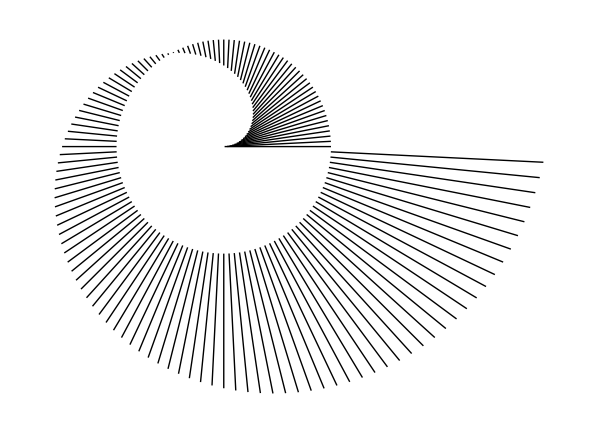

```mathematica
lines3[n_]:=Map[Line[{#[[1]],#[[2]]}]&,Table[{((3k+1)/n)ReIm[ⅇ^((k 2 Pi I)/n)],ReIm[ⅇ^((k 2 Pi I)/n)]},{k,0,n-1}]]
lines3[128]//toGL//Graphics
```

```mathematica
Integrate[Sin[x] x^2,{x,a,b}]
```

(-2+a^2) Cos[a]-(-2+b^2) Cos[b]-2 a Sin[a]+2 b Sin[b]

## Lines-UZT-3-Definition-for-KickOff

### Scaled

```mathematica
Graphics[{Disk[Scaled[{.25,.25}],1]},Frame->True,PlotRange->{{0,10},{0,10}}]
```

-Graphics-

```mathematica
Graphics[Disk[Scaled[{.50,.50}],10],PlotRange->{{-100,100},{-100,100}},Frame->True,AxesOrigin->{0,0},Axes->True]
```

-Graphics-

### Offset

## OLD-Preamble

```mathematica
(* AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace\\Geometry"];
<<Geometry` *)
```

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
<<TestAlgebra` 
<<Geometry`
```

Get::noopen: Cannot open TestAlgebra`.

$Failed

Get::noopen: Cannot open Geometry`.

$Failed

```mathematica
nCollatz[16]
```

{16,8,4,2,1}

## tmp-1

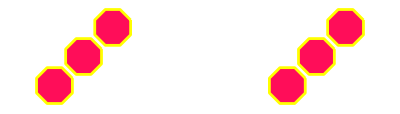

```mathematica
dpolyA:={tra3[newGeo[8,RGBColor[1,.05,.35,.1]][[1]],{1,1}],{Yellow,1,.005,2 π,2 π}}
dpolyA;
dpolyA//toGL;
{dpolyA,tra3[dpolyA,{2,2}]}//toGL ;
{dpolyA,tra3[dpolyA,{1.5,1.5}],tra3[dpolyA,{3.0,3.0}]}//toGL;
{{dpolyA,tra3[dpolyA,{1.5,1.5}],tra3[dpolyA,{3.0,3.0}]},tra3[{dpolyA,tra3[dpolyA,{1.5,1.5}],tra3[dpolyA,{3.0,3.0}]},{12,0}]}//toGL//gr
```

```mathematica
newGeo[1,Red,{{4,4}}]//toGL
```

newGeo[1,RGBColor[1, 0, 0],{{4,4}}]

```mathematica
{RGBColor[1, 0, 0],Opacity[1],{EdgeForm[{GrayLevel[0],Opacity[1],Thickness[0.05],Dashing[{2 π,2 π}]}],Polygon[…]}}//gr
```

-Graphics-

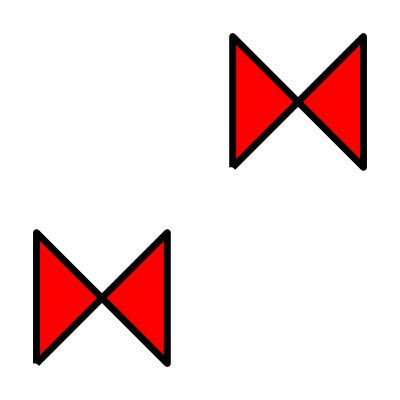

```mathematica
{newGeo[{1,{{0,0},{4,4},{4,0},{0,4}}}],tra3[newGeo[{1,{{0,0},{4,4},{4,0},{0,4}}}],{6,6}]}//toGL//gr
```

```mathematica
CoordinateTransformData[]//tf;
CoordinateChartData[]//tf
```

Bipolar
a | Euclidean | 2
BipolarCylindrical
a | Euclidean | 3
Bispherical
a | Euclidean | 3
Cartesian | Euclidean | 1
Cartesian | Euclidean | 2
Cartesian | Euclidean | 3
Cartesian | Euclidean | 4
Cartesian | Euclidean | 5
Cartesian | Euclidean | 6
Cartesian | Euclidean | 7
Cartesian | Euclidean | 8
Cartesian | Euclidean | 9
Cartesian | Euclidean | 10
CircularParabolic | Euclidean | 3
Confocal | 
α | β | Euclidean | 2
Confocal |  | 
α | β | γ | Euclidean | 3
Confocal |  |  | 
α_1 | α_2 | α_3 | α_4 | Euclidean | 4
Confocal |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | Euclidean | 5
Confocal |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | Euclidean | 6
Confocal |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | Euclidean | 7
Confocal |  |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | α_8 | Euclidean | 8
Confocal |  |  |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | α_8 | α_9 | Euclidean | 9
Confocal |  |  |  |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | α_8 | α_9 | α_10 | Euclidean | 10
Confocal |  |  |  |  |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | α_8 | α_9 | α_10 | α_11 | Euclidean | 11
ConfocalParaboloidal | 
α | β | Euclidean | 3
Conical | 
b | c | Euclidean | 3
Cylindrical | Euclidean | 3
Elliptic
a | Euclidean | 2
EllipticCylindrical
a | Euclidean | 3
Polar | Euclidean | 2
Hyperspherical | Euclidean | 3
Hyperspherical | Euclidean | 4
Hyperspherical | Euclidean | 5
Hyperspherical | Euclidean | 6
Hyperspherical | Euclidean | 7
Hyperspherical | Euclidean | 8
Hyperspherical | Euclidean | 9
Hyperspherical | Euclidean | 10
Hyperspherical | Euclidean | 11
OblateSpheroidal
a | Euclidean | 3
ParabolicCylindrical | Euclidean | 3
PlanarParabolic | Euclidean | 2
ProlateSpheroidal
a | Euclidean | 3
Spherical | Euclidean | 3
Toroidal
a | Euclidean | 3
Standard | Sphere
R | 1
Standard | Sphere
R | 2
Standard | Sphere
R | 3
Standard | Sphere
R | 4
Standard | Sphere
R | 5
Standard | Sphere
R | 6
Standard | Sphere
R | 7
Standard | Sphere
R | 8
Standard | Sphere
R | 9
Standard | Sphere
R | 10
Stereographic | Sphere
R | 1
Stereographic | Sphere
R | 2
Stereographic | Sphere
R | 3
Stereographic | Sphere
R | 4
Stereographic | Sphere
R | 5
Stereographic | Sphere
R | 6
Stereographic | Sphere
R | 7
Stereographic | Sphere
R | 8
Stereographic | Sphere
R | 9
Stereographic | Sphere
R | 10

```mathematica
CoordinateTransform[{"Cartesian"->"Polar",2},{1,-1}]
CoordinateTransform[{"Polar"->"Cartesian",2},{√2,-π/4}]
```

{√2,-π/4}

{1,-1}

```mathematica
FromPolarCoordinates[ToPolarCoordinates[{1/(√2),1/(√2)}]]
FromSphericalCoordinates[ToSphericalCoordinates[{{x,y,z},{1,0,0}}]]
```

{1/(√2),1/(√2)}

{{x,y,z},{1,0,0}}

```mathematica
CoordinateTransform[{"Cartesian"->"Polar",2},{1/√2,-1/√2}]
```

{1,-π/4}

```mathematica
1/((1/√2)+I(1/√2))
```

(1-ⅈ)/(√2)

```mathematica
FromPolarCoordinates[{R,θ}]
ToPolarCoordinates[FromPolarCoordinates[{R,θ}]]
ToPolarCoordinates[FromPolarCoordinates[{R,θ}]]//FullSimplify
```

{R Cos[θ],R Sin[θ]}

{√(R^2 Cos[θ]^2+R^2 Sin[θ]^2),ArcTan[R Cos[θ],R Sin[θ]]}

{√(R^2),ArcTan[R Cos[θ],R Sin[θ]]}

```mathematica
D[Exp[x],x]==Exp[x]
```

True

```mathematica
168-(18+17+15+13+12+15+14)-4
```

60

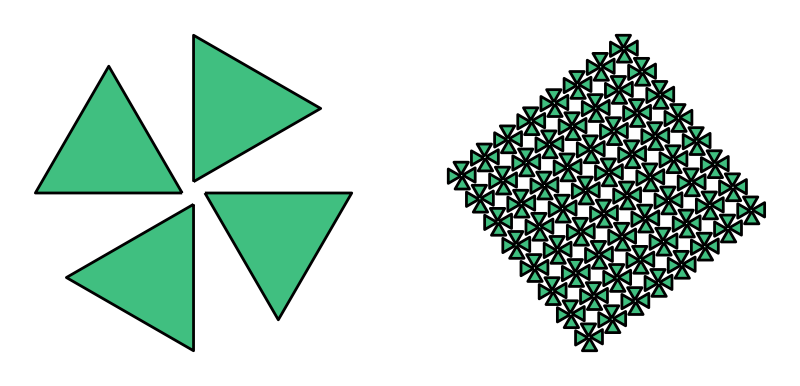

```mathematica
dpoly:={tra3[newGeo[3,RGBColor[.25,.75,.5,.5]][[1]],{1,1}],{Black,1,.005,2 π,2 π}}
GraphicsRow[{Graphics[Nest[teil,dpoly,1]//toGL],
Graphics[rot3[Nest[teil,dpoly,4],{30 Degree,{0,0}}]//toGL]}]
```

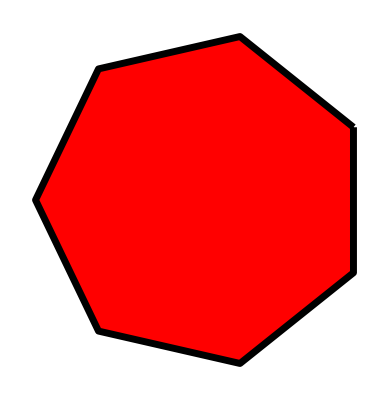

```mathematica
newGeo[7]//toGL//gr
```

```mathematica
nGonAtEdge3[fig_,{m_,n_}]:=trf3[
trf3[
newGeo[n],
toUnit[toEdges[newGeo[n]][[1,1,1,2]]]//N
],
toVector[toEdges[fig][[m,1,1,2]]]
]
```

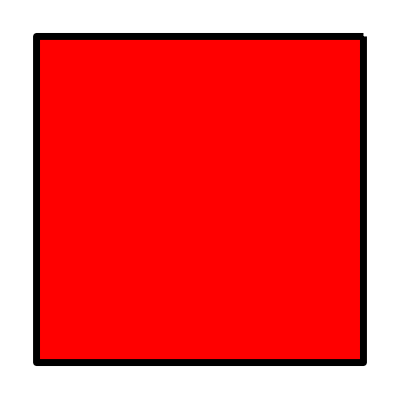

```mathematica
nGonAtEdge3[newGeo[4],{3,4}]//toGL//gr
```

## tmp-1.1

```mathematica
dpolyA:={tra3[newGeo[8,RGBColor[1,.05,.35,.1]][[1]],{1,1}],{Yellow,1,.005,2 π,2 π}}
dpolyA;
dpolyA//toGL;
{dpolyA,tra3[dpolyA,{2,2}]}//toGL ;
{dpolyA,tra3[dpolyA,{1.5,1.5}],tra3[dpolyA,{3.0,3.0}]}//toGL;
{{dpolyA,tra3[dpolyA,{1.5,1.5}],tra3[dpolyA,{3.0,3.0}]},tra3[{dpolyA,tra3[dpolyA,{1.5,1.5}],tra3[dpolyA,{3.0,3.0}]},{12,0}]}//toGL//gr
```

-Graphics-

```mathematica
newGeo[1,Red,{{4,4}}]//toGL
```

newGeo[1,RGBColor[1, 0, 0],{{4,4}}]

```mathematica
{RGBColor[1, 0, 0],Opacity[1],{EdgeForm[{GrayLevel[0],Opacity[1],Thickness[0.05],Dashing[{2 π,2 π}]}],Polygon[…]}}//gr
```

-Graphics-

```mathematica
{newGeo[{1,{{0,0},{4,4},{4,0},{0,4}}}],tra3[newGeo[{1,{{0,0},{4,4},{4,0},{0,4}}}],{6,6}]}//toGL//gr
```

-Graphics-

```mathematica
CoordinateTransformData[]//tf;
CoordinateChartData[]//tf
```

Bipolar
a | Euclidean | 2
BipolarCylindrical
a | Euclidean | 3
Bispherical
a | Euclidean | 3
Cartesian | Euclidean | 1
Cartesian | Euclidean | 2
Cartesian | Euclidean | 3
Cartesian | Euclidean | 4
Cartesian | Euclidean | 5
Cartesian | Euclidean | 6
Cartesian | Euclidean | 7
Cartesian | Euclidean | 8
Cartesian | Euclidean | 9
Cartesian | Euclidean | 10
CircularParabolic | Euclidean | 3
Confocal | 
α | β | Euclidean | 2
Confocal |  | 
α | β | γ | Euclidean | 3
Confocal |  |  | 
α_1 | α_2 | α_3 | α_4 | Euclidean | 4
Confocal |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | Euclidean | 5
Confocal |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | Euclidean | 6
Confocal |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | Euclidean | 7
Confocal |  |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | α_8 | Euclidean | 8
Confocal |  |  |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | α_8 | α_9 | Euclidean | 9
Confocal |  |  |  |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | α_8 | α_9 | α_10 | Euclidean | 10
Confocal |  |  |  |  |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | α_8 | α_9 | α_10 | α_11 | Euclidean | 11
ConfocalParaboloidal | 
α | β | Euclidean | 3
Conical | 
b | c | Euclidean | 3
Cylindrical | Euclidean | 3
Elliptic
a | Euclidean | 2
EllipticCylindrical
a | Euclidean | 3
Polar | Euclidean | 2
Hyperspherical | Euclidean | 3
Hyperspherical | Euclidean | 4
Hyperspherical | Euclidean | 5
Hyperspherical | Euclidean | 6
Hyperspherical | Euclidean | 7
Hyperspherical | Euclidean | 8
Hyperspherical | Euclidean | 9
Hyperspherical | Euclidean | 10
Hyperspherical | Euclidean | 11
OblateSpheroidal
a | Euclidean | 3
ParabolicCylindrical | Euclidean | 3
PlanarParabolic | Euclidean | 2
ProlateSpheroidal
a | Euclidean | 3
Spherical | Euclidean | 3
Toroidal
a | Euclidean | 3
Standard | Sphere
R | 1
Standard | Sphere
R | 2
Standard | Sphere
R | 3
Standard | Sphere
R | 4
Standard | Sphere
R | 5
Standard | Sphere
R | 6
Standard | Sphere
R | 7
Standard | Sphere
R | 8
Standard | Sphere
R | 9
Standard | Sphere
R | 10
Stereographic | Sphere
R | 1
Stereographic | Sphere
R | 2
Stereographic | Sphere
R | 3
Stereographic | Sphere
R | 4
Stereographic | Sphere
R | 5
Stereographic | Sphere
R | 6
Stereographic | Sphere
R | 7
Stereographic | Sphere
R | 8
Stereographic | Sphere
R | 9
Stereographic | Sphere
R | 10

```mathematica
CoordinateTransform[{"Cartesian"->"Polar",2},{1,-1}]
CoordinateTransform[{"Polar"->"Cartesian",2},{√2,-π/4}]
```

{√2,-π/4}

{1,-1}

```mathematica
FromPolarCoordinates[ToPolarCoordinates[{1/(√2),1/(√2)}]]
FromSphericalCoordinates[ToSphericalCoordinates[{{x,y,z},{1,0,0}}]]
```

{1/(√2),1/(√2)}

{{x,y,z},{1,0,0}}

```mathematica
CoordinateTransform[{"Cartesian"->"Polar",2},{1/√2,-1/√2}]
```

{1,-π/4}

```mathematica
1/((1/√2)+I(1/√2))
```

(1-ⅈ)/(√2)

```mathematica
FromPolarCoordinates[{R,θ}]
ToPolarCoordinates[FromPolarCoordinates[{R,θ}]]
ToPolarCoordinates[FromPolarCoordinates[{R,θ}]]//FullSimplify
```

{R Cos[θ],R Sin[θ]}

{√(R^2 Cos[θ]^2+R^2 Sin[θ]^2),ArcTan[R Cos[θ],R Sin[θ]]}

{√(R^2),ArcTan[R Cos[θ],R Sin[θ]]}

```mathematica
D[Exp[x],x]==Exp[x]
```

True

```mathematica
168-(18+17+15+13+12+15+14)-4
```

60

```mathematica
dpoly:={tra3[newGeo[3,RGBColor[.25,.75,.5,.5]][[1]],{1,1}],{Black,1,.005,2 π,2 π}}
GraphicsRow[{Graphics[Nest[teil,dpoly,1]//toGL],
Graphics[rot3[Nest[teil,dpoly,4],{30 Degree,{0,0}}]//toGL]}]
```

-Graphics-

```mathematica
newGeo[7]//toGL//gr
```

-Graphics-

```mathematica
nGonAtEdge3[fig_,{m_,n_}]:=trf3[
trf3[
newGeo[n],
toUnit[toEdges[newGeo[n]][[1,1,1,2]]]//N
],
toVector[toEdges[fig][[m,1,1,2]]]
]
```

```mathematica
nGonAtEdge3[newGeo[4],{3,4}]//toGL//gr
```

-Graphics-

```mathematica
newGeo[{1,{{2,2},{4,4},{0,4}}}]//toGL
```

{RGBColor[1, 0, 0],Opacity[1],{EdgeForm[{GrayLevel[0],Opacity[1],Thickness[0.0125],Dashing[{2 π,2 π}]}],Polygon[…]}}

```mathematica
EdgeForm[{GrayLevel[0],Opacity[1],Thickness[0.0125],Dashing[{2 π,2 π}]}]
```

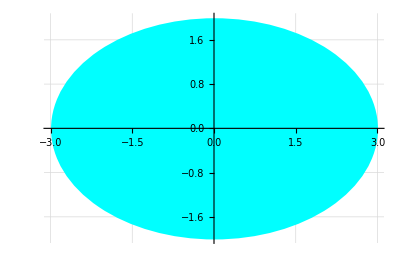

```mathematica
{Cyan,Ellipsoid[{0,0},{3,2}]}//gr1
```

```mathematica
EntityValue[
Entity["Country","Netherlands"],
EntityProperty["Country","Population"]
]
```

17591475 people

```mathematica
EntityValue[
Entity["Country","China"],
EntityProperty["Country","Population"]
]
```

1425700000 people

```mathematica
EntityValue[]
```

{AdministrativeDivision,Aircraft,Airline,Airport,AirportType,Alphabet,AmusementPark,AmusementParkRide,AmusementParkType,AnatomicalConceptIdentifier,AnatomicalFunctionalConcept,AnatomicalSpatialConcept,AnatomicalStructure,AnatomicalTemporalConcept,AnimalAnatomicalStructure,AnimalCoatColorAndPattern,AnimalEggColor,AnimalFeatherColor,AnimalSkinColor,AnimalUse,ArchitecturalStyle,Artwork,AstronomicalObservatory,AstronomicalRadioSource,AtmosphericLayer,AtomicLevel,AtomicLine,BasicFoodGroup,Beach,BioSequenceType,BoardGame,Book,Bridge,BridgeType,BroadcastStation,BroadcastStationClassification,Building,CalculusResult,Canal,Castle,CatBreed,CattleBreed,Cave,Cemetery,Character,Chemical,City,ClimateType,Cloud,CognitiveTask,Color,ColorSet,Comet,Company,ComputationalComplexityClass,Concept,Constellation,ConstructionMaterial,ContinuedFraction,ContinuedFractionResult,ContinuedFractionSource,Country,CrystalFamily,CrystallographicSpaceGroup,CrystalSystem,CurrencyDenomination,CurrencyDenominationType,Dam,DeepSpaceProbe,Desert,Digimon,Dinosaur,Disease,DisplayFormat,DistrictCourt,DogBreed,EarthImpact,Earthquake,EclipseType,ElectricalOutlet,Element,Emotion,EthnicGroup,Exoplanet,FamousChemistryProblem,FamousGem,FamousMathGame,FamousMathProblem,FamousPhysicsProblem,FAOConservationStatus,FictionalCharacter,FictionalPlace,FictionalSpecies,FileFormat,Financial,FiniteGroup,Flight,FlightStatus,Food,FoodAge,FoodAlcoholLabel,FoodBeefGrade,FoodBoneContent,FoodBrandName,FoodCaffeineLabel,FoodCalorieLabel,FoodComposition,FoodConcentration,FoodCrustType,FoodCulture,FoodDataSource,FoodFatLabel,FoodFatType,FoodFiberLabel,FoodFlavor,FoodGeometryType,FoodGlutenContent,FoodIntendedUse,FoodIronLabel,FoodLocation,FoodMaltType,FoodManufacturer,FoodMeatCut,FoodMeatQuality,FoodMoistureLevel,FoodNutritionalSupplement,FoodNutritionalSupplementNotAdded,FoodPackaging,FoodPart,FoodPattyCount,FoodPeelingType,FoodPreparation,FoodProcessingType,FoodSeafoodVariety,FoodSeedContent,FoodServingType,FoodShape,FoodSize,FoodSkinContent,FoodSodiumLabel,FoodState,FoodStorageType,FoodSubBrandName,FoodSugarLabel,FoodSugarType,FoodTexture,FoodTrimmingLevel,FoodType,FoodTypeGroup,FoodVariety,FoodVegetablePart,FoodYeastType,Forest,FrequencyAllocation,FunctionalAnalysisSource,FunctionSpace,Galaxy,Gender,Gene,GeneticTranslationTable,GeographicRegion,GeologicalLayer,GeologicalPeriod,GeometricScene,GivenName,Glacier,GlobalClimateData,GoatBreed,GrammaticalUnit,Graph,HistoricalCountry,HistoricalEvent,HistoricalPeriod,HistoricalSite,HorseBreed,HorseBreedConservationStatus,HorseCoatColorAndPattern,HorseType,HorseUse,ICDNine,ICDTen,Icon,IntegerSequence,InternetDomain,IPAddress,Island,ISO15924Group,Isotope,Knot,Lake,Lamina,Language,LanguageLocale,Laser,Lattice,LatticeSystem,LibraryBranch,LibrarySystem,LightColor,LunarInteriorLayer,MannedSpaceMission,MathematicalFunction,MathWorld,MatterPhase,MeasurementDevice,MedicalTest,MeteorShower,MetropolitanArea,MilitaryConflict,MilitaryConflictType,MilitaryFacilityType,Mine,Mineral,MinorPlanet,MoonPhase,Mountain,Movie,MPAARating,Museum,MusicAct,MusicAlbum,MusicAlbumRelease,MusicAlbumType,MusicalInstrument,MusicWork,MusicWorkRecording,MusicWorkRendition,Mythology,NaturalHazard,NaturalResource,NCBITranslationTableVersion,Nebula,Neighborhood,NetworkService,Neuron,NonperiodicTiling,NotableComputer,NuclearExplosion,NuclearExplosionType,NuclearReactor,NuclearReactorType,NuclearTestSite,Nutrient,ObjectStatus,Ocean,OilField,OperatingStatus,OrganizationType,Park,Particle,ParticleAccelerator,ParticulateMatter,Periodical,PeriodicTiling,Person,PersonTitle,PhysicalActivity,PhysicalConstant,PhysicalEffect,PhysicalQuantity,PhysicalSystem,PigBreed,PigeonBreed,PilatesExercise,PlaneCurve,Planet,PlanetaryMoon,Plant,Pokemon,PokemonAbilities,PokemonGeneration,PokemonPokedexColor,PokemonType,Polyhedron,PopularCurve,PoultryBreed,PoultryBreedConservationStatus,PreservationStatus,PrivateSchool,ProgrammingLanguage,Protein,PublicSchool,Pulsar,Reef,Religion,ReserveLand,RiemannHypothesisFormulation,River,Rocket,RocketFunction,Satellite,SchoolDistrict,SheepBreed,Ship,Shipwreck,SkinType,SNP,SolarSystemFeature,Solid,Sound,Source,SpaceCurve,Species,Sport,SportMatch,SportObject,Stadium,Star,StarCluster,StatisticalGroup,StormType,Supernova,SupernovaType,Surface,Surname,SystemModel,TaxonomicRank,TerrainType,TidalConstituent,TideStation,TimeZone,TopLevelDomain,TopologicalSpaceType,Transparency,TropicalStorm,Tunnel,UnderseaFeature,University,USCongressionalDistrict,USDAEggSize,USDAFoodGroup,VisualArtsArtForm,VisualArtsArtGenre,Volcano,Waterfall,WeatherStation,WeightTrainingExercise,WolframDemonstration,WolframLanguageSymbol,Word,WritingDirection,WritingScript,WritingScriptBaseline,WritingScriptLigature,WritingScriptStatus,WritingScriptType,WritingScriptWhiteSpace,YogaPose,YogaPosition,YogaProp,YogaSequence,ZIPCode}

```mathematica
EntityProperties["MusicAlbum"]
```

{label,tracklist,number of discs,number of songs,canonical release,release date,runtime,entity type list,image,artist,type,name,releases}

```mathematica
EntityValue[
Entity["MusicAlbum","Revolver"],
EntityProperty["MusicAlbum","artist"]
]
```

Missing[UnknownEntity,{MusicAlbum,Revolver}]

## tmp-Manikin

```mathematica
(*Define the head*)head=Sphere[{0,0,2},1];

(*Define the body*)
body=Cylinder[{{0,0,-1},{0,0,1}},0.6];

(*Define the arms*)
leftArm=Cylinder[{{-0.5,0,0},{-1.5,0,0}},0.2];
rightArm=Cylinder[{{0.5,0,0},{1.5,0,0}},0.2];

(*Define the legs*)
leftLeg=Cylinder[{{0,-0.5,-2},{0,-0.5,-3}},0.2];
rightLeg=Cylinder[{{0,0.5,-2},{0,0.5,-3}},0.2];

(*Combine all parts*)
manikin=Graphics3D[{head,body,leftArm,rightArm,leftLeg,rightLeg}];

(*Display the manikin*)
Show[manikin,ViewPoint->{0,Infinity,0}]
Show[manikin,ViewPoint->{0,0,Infinity}]
```

-Graphics3D-

-Graphics3D-

## tmp-2

```mathematica
Manipulate[
gHLinePD[p,q,Thickness->0.0075,Color->Blue]//toGL//grD
,
{{p,{0.6,0.2}},{-1,-1},{2,2},{0.1,0.1},Locator},
{{q,{0.4,0.4}},{-1,-1},{2,2},{0.1,0.1},Locator}
]
```

## Temp

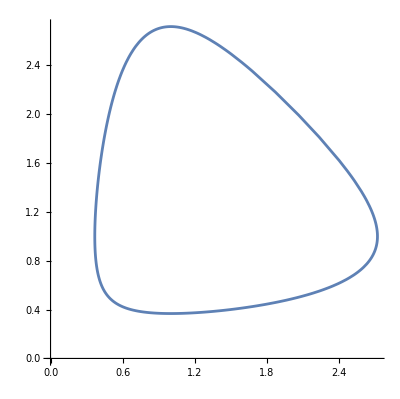

```mathematica
ParametricPlot[{E^Cos[t],E^Sin[t]},{t,0,2Pi}]
```

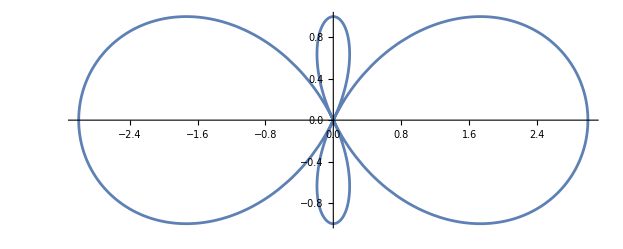

```mathematica
ParametricPlot[{(1+2Cos[2t]) Cos[t],(1+2Cos[2t]) Sin[t]},{t,0,2Pi}]
```

```mathematica
4!
```

24

```mathematica
Manipulate[
ListPlot[Map[ReIm[#[[1,2]]]&,Solve[z^n==pt.{1,I},z]],
AspectRatio->1,PlotRange->{{-1,1},{-1,1}}],
{n,2,128,1},
{{pt,{1,1}},Locator}
]
```

```mathematica
Manipulate[DynamicModule[{pt={{0,0}}},DynamicWrapper[LocatorPane[Dynamic[pt[[1;;nrPts]],(pt[[1;;nrPts]]=#)&],Dynamic[Graphics[{Red,PointSize[0.025],Point[pt]},PlotRange->{{-2,2},{-2,2}}]]],If[Length@pt<nrPts,pt=PadRight[pt,nrPts,{{0,0}}]]]],{nrPts,{1,2,3,4},SetterBar}]
```

```mathematica
DynamicModule[{pt={{0,0}}},Manipulate[Graphics[Point[pt],PlotRange->{{-1,1},{-1,1}}],Button["Add Locator",AppendTo[pt,{0,0}]],{{pt,pt},Locator,Appearance->None}]]
```

```mathematica
(2+3I)/Abs[2+3I]
```

```mathematica
Abs[(2+3 ⅈ)/(√13)]
```

1

## Temp-1

```mathematica
inv[p_]:=cnj3[mob[p,{{0,1},{1,0}}]]
```

```mathematica
m[p_]:=inv[p]
```

```mathematica
m[{0.1,0.1}]
```

{5.,5.}

```mathematica
m[{3,4}]
```

{3/25,4/25}

```mathematica
Exp[Cos[b]+I Sin[b]]//FullSimplify
Cos[b]+I Sin[b]//FullSimplify
Exp[a](Cos[b]+I Sin[b])//FullSimplify
```

ⅇ^(ⅇ^(ⅈ b))

ⅇ^(ⅈ b)

ⅇ^(a+ⅈ b)

```mathematica
Table[Integrate[Sin[x]^k,x],{k,1,24,2}]//tf
```

-Cos[x]
-(3 Cos[x])/4+1/12 Cos[3 x]
-(5 Cos[x])/8+5/48 Cos[3 x]-1/80 Cos[5 x]
-(35 Cos[x])/64+7/64 Cos[3 x]-7/320 Cos[5 x]+1/448 Cos[7 x]
-(63 Cos[x])/128+7/64 Cos[3 x]-9/320 Cos[5 x]+(9 Cos[7 x])/1792-Cos[9 x]/2304
-(231 Cos[x])/512+55/512 Cos[3 x]-(33 Cos[5 x])/1024+(55 Cos[7 x])/7168-(11 Cos[9 x])/9216+Cos[11 x]/11264
-(429 Cos[x])/1024+(429 Cos[3 x])/4096-(143 Cos[5 x])/4096+(143 Cos[7 x])/14336-(13 Cos[9 x])/6144+(13 Cos[11 x])/45056-Cos[13 x]/53248
-(6435 Cos[x])/16384+(5005 Cos[3 x])/49152-(3003 Cos[5 x])/81920+(195 Cos[7 x])/16384-(455 Cos[9 x])/147456+(105 Cos[11 x])/180224-(15 Cos[13 x])/212992+Cos[15 x]/245760
-(12155 Cos[x])/32768+(2431 Cos[3 x])/24576-(1547 Cos[5 x])/40960+(221 Cos[7 x])/16384-(595 Cos[9 x])/147456+(85 Cos[11 x])/90112-(17 Cos[13 x])/106496+(17 Cos[15 x])/983040-Cos[17 x]/1114112
-(46189 Cos[x])/131072+(12597 Cos[3 x])/131072-(12597 Cos[5 x])/327680+(969 Cos[7 x])/65536-(323 Cos[9 x])/65536+(969 Cos[11 x])/720896-(969 Cos[13 x])/3407872+(57 Cos[15 x])/1310720-(19 Cos[17 x])/4456448+Cos[19 x]/4980736
-(88179 Cos[x])/262144+(146965 Cos[3 x])/1572864-(20349 Cos[5 x])/524288+(14535 Cos[7 x])/917504-(2261 Cos[9 x])/393216+(20349 Cos[11 x])/11534336-(5985 Cos[13 x])/13631488+(133 Cos[15 x])/1572864-(105 Cos[17 x])/8912896+(21 Cos[19 x])/19922944-Cos[21 x]/22020096
-(676039 Cos[x])/2097152+(572033 Cos[3 x])/6291456-(81719 Cos[5 x])/2097152+(245157 Cos[7 x])/14680064-(81719 Cos[9 x])/12582912+(9177 Cos[11 x])/4194304-(33649 Cos[13 x])/54525952+(1771 Cos[15 x])/12582912-(1771 Cos[17 x])/71303168+(253 Cos[19 x])/79691776-(23 Cos[21 x])/88080384+Cos[23 x]/96468992

```mathematica
FactorInteger[{80,320,320,1024}]//tf
```

2
4 | 5
1
2
6 | 5
1
2
6 | 5
1
2
10 |

## Hermitian Matrix ( check this ... )

```mathematica
m=1/√2{{1,-I},{I,1}};
```

```mathematica
m//mf
```

(1/(√2) | -ⅈ/(√2)
ⅈ/(√2) | 1/(√2))

```mathematica
ConjugateTranspose[m]//mf
```

(1/(√2) | -ⅈ/(√2)
ⅈ/(√2) | 1/(√2))

```mathematica
m.ConjugateTranspose[m]
```

{{1,-ⅈ},{ⅈ,1}}

```mathematica
HermitianMatrixQ[m]
```

True

```mathematica
a=p;b=q;c=r;d=s;
f1[z_]:=z+d/c
f2[z_]:=1/z
f3[z_]:=(-(a*d - b*c)/c^2)z
f4[z_]:=z+a/c
```

```mathematica
f4[f3[f2[f1[z]]]]//FullSimplify
```

(q+p z)/(s+r z)

```mathematica
m1:={{1,d/c},{0,1}}
m2:={{0,1},{1,0}}
m3:={{-(a*d - b*c)/c^2,0},{0,1}}
m4:={{1,a/c},{0,1}}
```

```mathematica
m4.m3.m2.m1//mf//FullSimplify
```

(p/r | q/r
1 | s/r)

```mathematica
m1.{1,1}
```

{1+s/r,1}

```mathematica
mob[{1,0},m2.m1]
```

{1/(1+s/r)^2+s/(r (1+s/r)^2),0}

## Cycloids and more ...

```mathematica
Manipulate[
ParametricPlot[{2+2 Cos[a t]+ Cos[b t],2+2 Sin[c t]- Sin[d t]},{t,0,2 Pi},PlotStyle->Thick ],
{a,1,18,1},
{b,1,18,1},
{c,1,18,1},
{d,1,18,1}
]
```

```mathematica
18^4
```

104976

## Möbius Transformations

### AI shit from Bing and Bard

```mathematica
a=1;
b=2+I;
c=3+3I;
p=1+I;
q=4+2I;
r=6+3I;
mb1[z_]:=((z-a)(b-c))/((z-c)(b-a))
mb2[z_]:=r+(q-r)/(z-p)
mb3[z_]:=mb2[mb1[z]]
mb3[z_]:=(a-p)(r-q)z+((b-q)(p-r))/((a-p)(c-r))z+(b-q)(c-p)
```

```mathematica
mb3[a]
```

2-(32 ⅈ)/3

```mathematica
15/2.
```

7.5

```mathematica
Rationalize[7.51]
```

751/100

```mathematica
ToSphericalCoordinates[{12,12,0}]
```

{12 √2,π/2,π/4}

### Another Try...

```mathematica
50000/12*0.02
```

83.3333

```mathematica
ClearAll[a,b,c,p,q,r]
```

```mathematica
Apply[Complex,{0,1}]
```

ⅈ

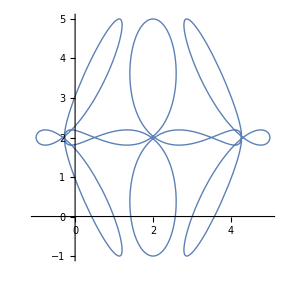
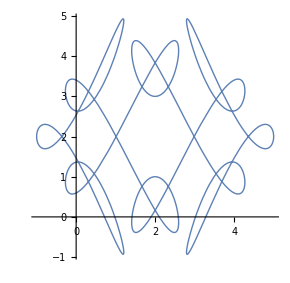

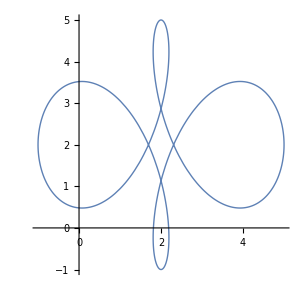
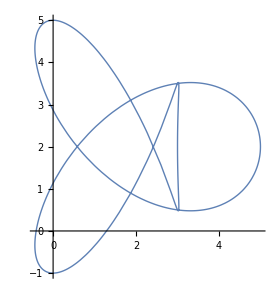

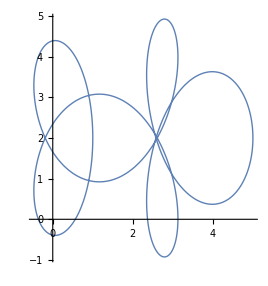
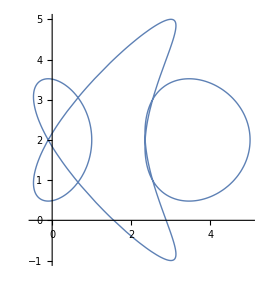

```mathematica
Manipulate[
ParametricPlot[{Cos[t](2+Cos[a t] Cos[b t]),Sin[t](2+Cos[c t] Sin[d t])},{t,0,2 Pi},PlotStyle->Thick ,Axes->False],
{a,1,18,1},
{b,1,18,1},
{c,1,18,1},
{d,1,18,1}
]
```

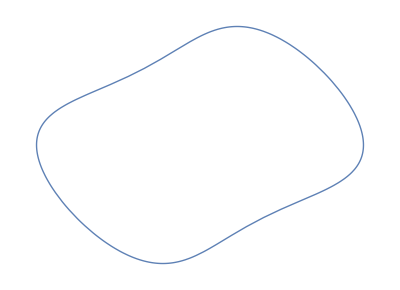

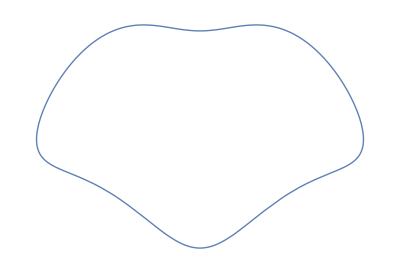

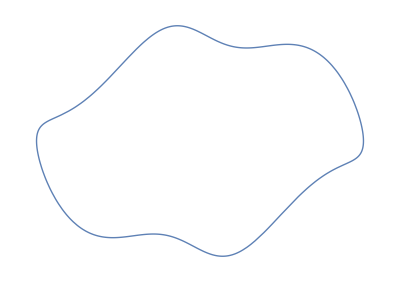

## Temp-2

```mathematica
mt:={{1+I,I},{-I,1-I}}
mob[mob[mob[mob[mob[{0.6,0.2},mt],mt],mt],mt],mt]
```

{-0.976471,0.194118}

## entity system

```mathematica
EntityValue[]
```

{AdministrativeDivision,Aircraft,Airline,Airport,AirportType,Alphabet,AmusementPark,AmusementParkRide,AmusementParkType,AnatomicalConceptIdentifier,AnatomicalFunctionalConcept,AnatomicalSpatialConcept,AnatomicalStructure,AnatomicalTemporalConcept,AnimalAnatomicalStructure,AnimalCoatColorAndPattern,AnimalEggColor,AnimalFeatherColor,AnimalSkinColor,AnimalUse,ArchitecturalStyle,Artwork,AstronomicalObservatory,AstronomicalRadioSource,AtmosphericLayer,AtomicLevel,AtomicLine,BasicFoodGroup,Beach,BioSequenceType,BoardGame,Book,Bridge,BridgeType,BroadcastStation,BroadcastStationClassification,Building,CalculusResult,Canal,Castle,CatBreed,CattleBreed,Cave,Cemetery,Character,Chemical,City,ClimateType,Cloud,CognitiveTask,Color,ColorSet,Comet,Company,ComputationalComplexityClass,Concept,Constellation,ConstructionMaterial,ContinuedFraction,ContinuedFractionResult,ContinuedFractionSource,Country,CrystalFamily,CrystallographicSpaceGroup,CrystalSystem,CurrencyDenomination,CurrencyDenominationType,Dam,DeepSpaceProbe,Desert,Digimon,Dinosaur,Disease,DisplayFormat,DistrictCourt,DogBreed,EarthImpact,Earthquake,EclipseType,ElectricalOutlet,Element,Emotion,EthnicGroup,Exoplanet,FamousChemistryProblem,FamousGem,FamousMathGame,FamousMathProblem,FamousPhysicsProblem,FAOConservationStatus,FictionalCharacter,FictionalPlace,FictionalSpecies,FileFormat,Financial,FiniteGroup,Flight,FlightStatus,Food,FoodAge,FoodAlcoholLabel,FoodBeefGrade,FoodBoneContent,FoodBrandName,FoodCaffeineLabel,FoodCalorieLabel,FoodComposition,FoodConcentration,FoodCrustType,FoodCulture,FoodDataSource,FoodFatLabel,FoodFatType,FoodFiberLabel,FoodFlavor,FoodGeometryType,FoodGlutenContent,FoodIntendedUse,FoodIronLabel,FoodLocation,FoodMaltType,FoodManufacturer,FoodMeatCut,FoodMeatQuality,FoodMoistureLevel,FoodNutritionalSupplement,FoodNutritionalSupplementNotAdded,FoodPackaging,FoodPart,FoodPattyCount,FoodPeelingType,FoodPreparation,FoodProcessingType,FoodSeafoodVariety,FoodSeedContent,FoodServingType,FoodShape,FoodSize,FoodSkinContent,FoodSodiumLabel,FoodState,FoodStorageType,FoodSubBrandName,FoodSugarLabel,FoodSugarType,FoodTexture,FoodTrimmingLevel,FoodType,FoodTypeGroup,FoodVariety,FoodVegetablePart,FoodYeastType,Forest,FrequencyAllocation,FunctionalAnalysisSource,FunctionSpace,Galaxy,Gender,Gene,GeneticTranslationTable,GeographicRegion,GeologicalLayer,GeologicalPeriod,GeometricScene,GivenName,Glacier,GlobalClimateData,GoatBreed,GrammaticalUnit,Graph,HistoricalCountry,HistoricalEvent,HistoricalPeriod,HistoricalSite,HorseBreed,HorseBreedConservationStatus,HorseCoatColorAndPattern,HorseType,HorseUse,ICDNine,ICDTen,Icon,IntegerSequence,InternetDomain,IPAddress,Island,ISO15924Group,Isotope,Knot,Lake,Lamina,Language,LanguageLocale,Laser,Lattice,LatticeSystem,LibraryBranch,LibrarySystem,LightColor,LunarInteriorLayer,MannedSpaceMission,MathematicalFunction,MathWorld,MatterPhase,MeasurementDevice,MedicalTest,MeteorShower,MetropolitanArea,MilitaryConflict,MilitaryConflictType,MilitaryFacilityType,Mine,Mineral,MinorPlanet,MoonPhase,Mountain,Movie,MPAARating,Museum,MusicAct,MusicAlbum,MusicAlbumRelease,MusicAlbumType,MusicalInstrument,MusicWork,MusicWorkRecording,MusicWorkRendition,Mythology,NaturalHazard,NaturalResource,NCBITranslationTableVersion,Nebula,Neighborhood,NetworkService,Neuron,NonperiodicTiling,NotableComputer,NuclearExplosion,NuclearExplosionType,NuclearReactor,NuclearReactorType,NuclearTestSite,Nutrient,ObjectStatus,Ocean,OilField,OperatingStatus,OrganizationType,Park,Particle,ParticleAccelerator,ParticulateMatter,Periodical,PeriodicTiling,Person,PersonTitle,PhysicalActivity,PhysicalConstant,PhysicalEffect,PhysicalQuantity,PhysicalSystem,PigBreed,PigeonBreed,PilatesExercise,PlaneCurve,Planet,PlanetaryMoon,Plant,Pokemon,PokemonAbilities,PokemonGeneration,PokemonPokedexColor,PokemonType,Polyhedron,PopularCurve,PoultryBreed,PoultryBreedConservationStatus,PreservationStatus,PrivateSchool,ProgrammingLanguage,Protein,PublicSchool,Pulsar,Reef,Religion,ReserveLand,RiemannHypothesisFormulation,River,Rocket,RocketFunction,Satellite,SchoolDistrict,SheepBreed,Ship,Shipwreck,SkinType,SNP,SolarSystemFeature,Solid,Sound,Source,SpaceCurve,Species,Sport,SportMatch,SportObject,Stadium,Star,StarCluster,StatisticalGroup,StormType,Supernova,SupernovaType,Surface,Surname,SystemModel,TaxonomicRank,TerrainType,TidalConstituent,TideStation,TimeZone,TopLevelDomain,TopologicalSpaceType,Transparency,TropicalStorm,Tunnel,UnderseaFeature,University,USCongressionalDistrict,USDAEggSize,USDAFoodGroup,VisualArtsArtForm,VisualArtsArtGenre,Volcano,Waterfall,WeatherStation,WeightTrainingExercise,WolframDemonstration,WolframLanguageSymbol,Word,WritingDirection,WritingScript,WritingScriptBaseline,WritingScriptLigature,WritingScriptStatus,WritingScriptType,WritingScriptWhiteSpace,YogaPose,YogaPosition,YogaProp,YogaSequence,ZIPCode}

```mathematica
lst=%;
```

```mathematica
lst
```

{AdministrativeDivision,Aircraft,Airline,Airport,AirportType,Alphabet,AmusementPark,AmusementParkRide,AmusementParkType,AnatomicalConceptIdentifier,AnatomicalFunctionalConcept,AnatomicalSpatialConcept,AnatomicalStructure,AnatomicalTemporalConcept,AnimalAnatomicalStructure,AnimalCoatColorAndPattern,AnimalEggColor,AnimalFeatherColor,AnimalSkinColor,AnimalUse,ArchitecturalStyle,Artwork,AstronomicalObservatory,AstronomicalRadioSource,AtmosphericLayer,AtomicLevel,AtomicLine,BasicFoodGroup,Beach,BioSequenceType,BoardGame,Book,Bridge,BridgeType,BroadcastStation,BroadcastStationClassification,Building,CalculusResult,Canal,Castle,CatBreed,CattleBreed,Cave,Cemetery,Character,Chemical,City,ClimateType,Cloud,CognitiveTask,Color,ColorSet,Comet,Company,ComputationalComplexityClass,Concept,Constellation,ConstructionMaterial,ContinuedFraction,ContinuedFractionResult,ContinuedFractionSource,Country,CrystalFamily,CrystallographicSpaceGroup,CrystalSystem,CurrencyDenomination,CurrencyDenominationType,Dam,DeepSpaceProbe,Desert,Digimon,Dinosaur,Disease,DisplayFormat,DistrictCourt,DogBreed,EarthImpact,Earthquake,EclipseType,ElectricalOutlet,Element,Emotion,EthnicGroup,Exoplanet,FamousChemistryProblem,FamousGem,FamousMathGame,FamousMathProblem,FamousPhysicsProblem,FAOConservationStatus,FictionalCharacter,FictionalPlace,FictionalSpecies,FileFormat,Financial,FiniteGroup,Flight,FlightStatus,Food,FoodAge,FoodAlcoholLabel,FoodBeefGrade,FoodBoneContent,FoodBrandName,FoodCaffeineLabel,FoodCalorieLabel,FoodComposition,FoodConcentration,FoodCrustType,FoodCulture,FoodDataSource,FoodFatLabel,FoodFatType,FoodFiberLabel,FoodFlavor,FoodGeometryType,FoodGlutenContent,FoodIntendedUse,FoodIronLabel,FoodLocation,FoodMaltType,FoodManufacturer,FoodMeatCut,FoodMeatQuality,FoodMoistureLevel,FoodNutritionalSupplement,FoodNutritionalSupplementNotAdded,FoodPackaging,FoodPart,FoodPattyCount,FoodPeelingType,FoodPreparation,FoodProcessingType,FoodSeafoodVariety,FoodSeedContent,FoodServingType,FoodShape,FoodSize,FoodSkinContent,FoodSodiumLabel,FoodState,FoodStorageType,FoodSubBrandName,FoodSugarLabel,FoodSugarType,FoodTexture,FoodTrimmingLevel,FoodType,FoodTypeGroup,FoodVariety,FoodVegetablePart,FoodYeastType,Forest,FrequencyAllocation,FunctionalAnalysisSource,FunctionSpace,Galaxy,Gender,Gene,GeneticTranslationTable,GeographicRegion,GeologicalLayer,GeologicalPeriod,GeometricScene,GivenName,Glacier,GlobalClimateData,GoatBreed,GrammaticalUnit,Graph,HistoricalCountry,HistoricalEvent,HistoricalPeriod,HistoricalSite,HorseBreed,HorseBreedConservationStatus,HorseCoatColorAndPattern,HorseType,HorseUse,ICDNine,ICDTen,Icon,IntegerSequence,InternetDomain,IPAddress,Island,ISO15924Group,Isotope,Knot,Lake,Lamina,Language,LanguageLocale,Laser,Lattice,LatticeSystem,LibraryBranch,LibrarySystem,LightColor,LunarInteriorLayer,MannedSpaceMission,MathematicalFunction,MathWorld,MatterPhase,MeasurementDevice,MedicalTest,MeteorShower,MetropolitanArea,MilitaryConflict,MilitaryConflictType,MilitaryFacilityType,Mine,Mineral,MinorPlanet,MoonPhase,Mountain,Movie,MPAARating,Museum,MusicAct,MusicAlbum,MusicAlbumRelease,MusicAlbumType,MusicalInstrument,MusicWork,MusicWorkRecording,MusicWorkRendition,Mythology,NaturalHazard,NaturalResource,NCBITranslationTableVersion,Nebula,Neighborhood,NetworkService,Neuron,NonperiodicTiling,NotableComputer,NuclearExplosion,NuclearExplosionType,NuclearReactor,NuclearReactorType,NuclearTestSite,Nutrient,ObjectStatus,Ocean,OilField,OperatingStatus,OrganizationType,Park,Particle,ParticleAccelerator,ParticulateMatter,Periodical,PeriodicTiling,Person,PersonTitle,PhysicalActivity,PhysicalConstant,PhysicalEffect,PhysicalQuantity,PhysicalSystem,PigBreed,PigeonBreed,PilatesExercise,PlaneCurve,Planet,PlanetaryMoon,Plant,Pokemon,PokemonAbilities,PokemonGeneration,PokemonPokedexColor,PokemonType,Polyhedron,PopularCurve,PoultryBreed,PoultryBreedConservationStatus,PreservationStatus,PrivateSchool,ProgrammingLanguage,Protein,PublicSchool,Pulsar,Reef,Religion,ReserveLand,RiemannHypothesisFormulation,River,Rocket,RocketFunction,Satellite,SchoolDistrict,SheepBreed,Ship,Shipwreck,SkinType,SNP,SolarSystemFeature,Solid,Sound,Source,SpaceCurve,Species,Sport,SportMatch,SportObject,Stadium,Star,StarCluster,StatisticalGroup,StormType,Supernova,SupernovaType,Surface,Surname,SystemModel,TaxonomicRank,TerrainType,TidalConstituent,TideStation,TimeZone,TopLevelDomain,TopologicalSpaceType,Transparency,TropicalStorm,Tunnel,UnderseaFeature,University,USCongressionalDistrict,USDAEggSize,USDAFoodGroup,VisualArtsArtForm,VisualArtsArtGenre,Volcano,Waterfall,WeatherStation,WeightTrainingExercise,WolframDemonstration,WolframLanguageSymbol,Word,WritingDirection,WritingScript,WritingScriptBaseline,WritingScriptLigature,WritingScriptStatus,WritingScriptType,WritingScriptWhiteSpace,YogaPose,YogaPosition,YogaProp,YogaSequence,ZIPCode}

```mathematica
EntityValue[Entity["PlanetaryMoon","Titan"],"Gravity"]
```

1.3532 m/s^2

```mathematica
EntityValue["MathWorld","Entities"]
(*
EntityValue["PlanetaryMoon","Properties"]
EntityValue["Planet","EntityClasses"]
EntityValue["Planet","PropertyClasses"]
*)
```

```mathematica
lst1=%;
```

```mathematica
lst1//Length
```

13922

```mathematica
lst//tf
```

AdministrativeDivision
Aircraft
Airline
Airport
AirportType
Alphabet
AmusementPark
AmusementParkRide
AmusementParkType
AnatomicalConceptIdentifier
AnatomicalFunctionalConcept
AnatomicalSpatialConcept
AnatomicalStructure
AnatomicalTemporalConcept
AnimalAnatomicalStructure
AnimalCoatColorAndPattern
AnimalEggColor
AnimalFeatherColor
AnimalSkinColor
AnimalUse
ArchitecturalStyle
Artwork
AstronomicalObservatory
AstronomicalRadioSource
AtmosphericLayer
AtomicLevel
AtomicLine
BasicFoodGroup
Beach
BioSequenceType
BoardGame
Book
Bridge
BridgeType
BroadcastStation
BroadcastStationClassification
Building
CalculusResult
Canal
Castle
CatBreed
CattleBreed
Cave
Cemetery
Character
Chemical
City
ClimateType
Cloud
CognitiveTask
Color
ColorSet
Comet
Company
ComputationalComplexityClass
Concept
Constellation
ConstructionMaterial
ContinuedFraction
ContinuedFractionResult
ContinuedFractionSource
Country
CrystalFamily
CrystallographicSpaceGroup
CrystalSystem
CurrencyDenomination
CurrencyDenominationType
Dam
DeepSpaceProbe
Desert
Digimon
Dinosaur
Disease
DisplayFormat
DistrictCourt
DogBreed
EarthImpact
Earthquake
EclipseType
ElectricalOutlet
Element
Emotion
EthnicGroup
Exoplanet
FamousChemistryProblem
FamousGem
FamousMathGame
FamousMathProblem
FamousPhysicsProblem
FAOConservationStatus
FictionalCharacter
FictionalPlace
FictionalSpecies
FileFormat
Financial
FiniteGroup
Flight
FlightStatus
Food
FoodAge
FoodAlcoholLabel
FoodBeefGrade
FoodBoneContent
FoodBrandName
FoodCaffeineLabel
FoodCalorieLabel
FoodComposition
FoodConcentration
FoodCrustType
FoodCulture
FoodDataSource
FoodFatLabel
FoodFatType
FoodFiberLabel
FoodFlavor
FoodGeometryType
FoodGlutenContent
FoodIntendedUse
FoodIronLabel
FoodLocation
FoodMaltType
FoodManufacturer
FoodMeatCut
FoodMeatQuality
FoodMoistureLevel
FoodNutritionalSupplement
FoodNutritionalSupplementNotAdded
FoodPackaging
FoodPart
FoodPattyCount
FoodPeelingType
FoodPreparation
FoodProcessingType
FoodSeafoodVariety
FoodSeedContent
FoodServingType
FoodShape
FoodSize
FoodSkinContent
FoodSodiumLabel
FoodState
FoodStorageType
FoodSubBrandName
FoodSugarLabel
FoodSugarType
FoodTexture
FoodTrimmingLevel
FoodType
FoodTypeGroup
FoodVariety
FoodVegetablePart
FoodYeastType
Forest
FrequencyAllocation
FunctionalAnalysisSource
FunctionSpace
Galaxy
Gender
Gene
GeneticTranslationTable
GeographicRegion
GeologicalLayer
GeologicalPeriod
GeometricScene
GivenName
Glacier
GlobalClimateData
GoatBreed
GrammaticalUnit
Graph
HistoricalCountry
HistoricalEvent
HistoricalPeriod
HistoricalSite
HorseBreed
HorseBreedConservationStatus
HorseCoatColorAndPattern
HorseType
HorseUse
ICDNine
ICDTen
Icon
IntegerSequence
InternetDomain
IPAddress
Island
ISO15924Group
Isotope
Knot
Lake
Lamina
Language
LanguageLocale
Laser
Lattice
LatticeSystem
LibraryBranch
LibrarySystem
LightColor
LunarInteriorLayer
MannedSpaceMission
MathematicalFunction
MathWorld
MatterPhase
MeasurementDevice
MedicalTest
MeteorShower
MetropolitanArea
MilitaryConflict
MilitaryConflictType
MilitaryFacilityType
Mine
Mineral
MinorPlanet
MoonPhase
Mountain
Movie
MPAARating
Museum
MusicAct
MusicAlbum
MusicAlbumRelease
MusicAlbumType
MusicalInstrument
MusicWork
MusicWorkRecording
MusicWorkRendition
Mythology
NaturalHazard
NaturalResource
NCBITranslationTableVersion
Nebula
Neighborhood
NetworkService
Neuron
NonperiodicTiling
NotableComputer
NuclearExplosion
NuclearExplosionType
NuclearReactor
NuclearReactorType
NuclearTestSite
Nutrient
ObjectStatus
Ocean
OilField
OperatingStatus
OrganizationType
Park
Particle
ParticleAccelerator
ParticulateMatter
Periodical
PeriodicTiling
Person
PersonTitle
PhysicalActivity
PhysicalConstant
PhysicalEffect
PhysicalQuantity
PhysicalSystem
PigBreed
PigeonBreed
PilatesExercise
PlaneCurve
Planet
PlanetaryMoon
Plant
Pokemon
PokemonAbilities
PokemonGeneration
PokemonPokedexColor
PokemonType
Polyhedron
PopularCurve
PoultryBreed
PoultryBreedConservationStatus
PreservationStatus
PrivateSchool
ProgrammingLanguage
Protein
PublicSchool
Pulsar
Reef
Religion
ReserveLand
RiemannHypothesisFormulation
River
Rocket
RocketFunction
Satellite
SchoolDistrict
SheepBreed
Ship
Shipwreck
SkinType
SNP
SolarSystemFeature
Solid
Sound
Source
SpaceCurve
Species
Sport
SportMatch
SportObject
Stadium
Star
StarCluster
StatisticalGroup
StormType
Supernova
SupernovaType
Surface
Surname
SystemModel
TaxonomicRank
TerrainType
TidalConstituent
TideStation
TimeZone
TopLevelDomain
TopologicalSpaceType
Transparency
TropicalStorm
Tunnel
UnderseaFeature
University
USCongressionalDistrict
USDAEggSize
USDAFoodGroup
VisualArtsArtForm
VisualArtsArtGenre
Volcano
Waterfall
WeatherStation
WeightTrainingExercise
WolframDemonstration
WolframLanguageSymbol
Word
WritingDirection
WritingScript
WritingScriptBaseline
WritingScriptLigature
WritingScriptStatus
WritingScriptType
WritingScriptWhiteSpace
YogaPose
YogaPosition
YogaProp
YogaSequence
ZIPCode

```mathematica
lst1//tf
```

## GyroGroups and Hyperbolic Geometry

## Study-notes

```mathematica
f1[z_,{{a_,b_},{c_,d_}}]:=(a z + b)/(c z + d)
f2[z_,{{a_,b_},{c_,d_}}]:=(d/(-b c+a d) z-b/(-b c+a d))/(-c/(-b c+a d) z+a/(-b c+a d))
m:={{2,1},{1,1}}
```

```mathematica
f1[I/2,m]
```

43/17+(2 ⅈ)/17

```mathematica
f2[43/17+(2 ⅈ)/17,m]
```

ⅈ/2

```mathematica
(2+3I)(2-3I)
```

13

```mathematica
Abs[2+3I]^2
```

13

```mathematica
val=0.6+0.2I;
f1[val,m]
f2[f1[val,m],m]
```

1.38462+0.0769231 ⅈ

0.6+0.2 ⅈ

```mathematica
a=2+2I;
c=-2+2I;
Mod[Arg[a/c],2Pi]
```

(3 π)/2